```mathematica
Sum[(-t/n)^i,{i,2,Infinity}]
```

t^2/(n (n+t))

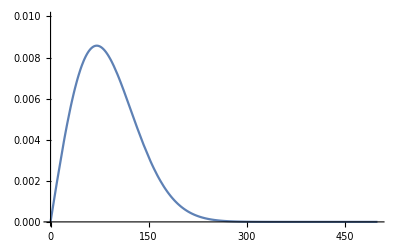

```mathematica
With[{pop=1000,r=0.1},Plot[{2r/pop*t*Exp[-r/pop*t^2]},{t,0,500},PlotRange->{0,0.01}]]
```

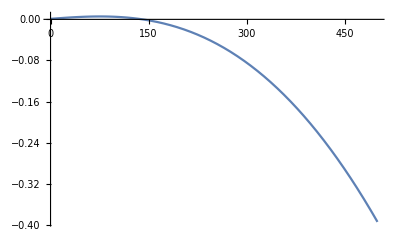

```mathematica
With[{pop=1000,r=0.1},Plot[{(r t+1)/pop(Exp[-t/pop]-r t^2/2/(pop+t))},{t,0,500},PlotRange->All]]
```

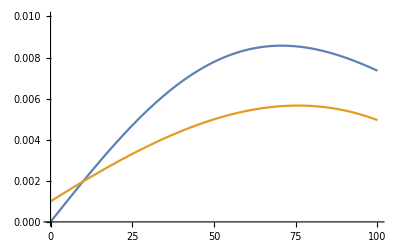

```mathematica
With[{pop=1000,r=0.1},Plot[{2r/pop*t*Exp[-r/pop*t^2],(r t+1)/pop(Exp[-t/pop]-r t^2/2/(pop+t))},{t,0,100},PlotRange->{0,0.01}]]
```